```mathematica
ClearAll["Global`*"];
```

```mathematica
f[x_]=√x-2*Cos[x];
```

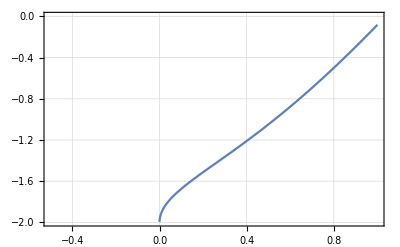

```mathematica
Plot[√x-2*Cos[x],{x,-0.5,1}, Frame->True,GridLines->Automatic]
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
(*Метод секущих*)
```

```mathematica
Secuch[a_, b_]:=(
x[0]=a;
x[1]=b;
n=0;
eps=0.001;
ep=1;
Print["Начало: ", a, "; Конец: ", b];
Print["n= ", n, " x= ", x[n], " f[x]= ", N[f[x[n]]], " dx= ", ep];
n++;
Print["n= ", n, " x= ", x[n], " f[x]= ", N[f[x[n]]], " dx= ", ep];
While[ep > eps, x[n+1] = x[n]-N[f[x[n]]*(x[n]-x[n-1])/(f[x[n]]-f[x[n-1]])];
ep=Abs[x[n+1]-x[n]];
n++;Print["n= ", n, " x= ", x[n], " f[x]= ", N[f[x[n]]], " dx= ", ep]];
);
```

```mathematica
Secuch[-0.5, 0.5]
Secuch[0.75, 0.9]
Secuch[0.95, 1.05]
```

Начало: -0.5; Конец: 0.5

n= 0 x= -0.5 f[x]= f[-0.5] dx= 1

n= 1 x= 0.5 f[x]= f[0.5] dx= 1

n= 2 x= 0.5-(1. f[0.5])/(-1. f[-0.5]+f[0.5]) f[x]= f[0.5-(1. f[0.5])/(-1. f[-0.5]+f[0.5])] dx= Abs[0.-(1. f[0.5])/(-1. f[-0.5]+f[0.5])]

Начало: 0.75; Конец: 0.9

n= 0 x= 0.75 f[x]= f[0.75] dx= 1

n= 1 x= 0.9 f[x]= f[0.9] dx= 1

n= 2 x= 0.9-(0.15 f[0.9])/(-1. f[0.75]+f[0.9]) f[x]= f[0.9-(0.15 f[0.9])/(-1. f[0.75]+f[0.9])] dx= Abs[0.-(0.15 f[0.9])/(-1. f[0.75]+f[0.9])]

Начало: 0.95; Конец: 1.05

n= 0 x= 0.95 f[x]= f[0.95] dx= 1

n= 1 x= 1.05 f[x]= f[1.05] dx= 1

n= 2 x= 1.05-(0.1 f[1.05])/(-1. f[0.95]+f[1.05]) f[x]= f[1.05-(0.1 f[1.05])/(-1. f[0.95]+f[1.05])] dx= Abs[0.-(0.1 f[1.05])/(-1. f[0.95]+f[1.05])]

```mathematica
ClearAll["Global`*"];
```

```mathematica
(*Комбинированный метод*)
```

```mathematica
f[x_]=√x-2*Cos[x];
```

```mathematica
f1[x_]=Dt[f[x],x]
```

1/(2 √x)+2 Sin[x]

```mathematica
f2[x_]=Dt[f[x],{x,2}]
```

-1/(4 x^(3/2))+2 Cos[x]

```mathematica
N[f2[1]*f[1]]
```

-0.0669506

```mathematica
z0=-0.5;
z1=1;
x=1;
n=0;
eps=0.001;
ep=1;
Print["n = ", n, " x = ", x, " z1 = ", z1, " delX = ", ep];
While[ep>eps,z1=N[z1-f[z1]*(z0-z1)/(f[z0]-f[z1])];x=N[x-f[x]/f1[x]];ep=Abs[z1-x];z0=x;n++;
Print["n = ", n, " x = ", x, " z1 = ", z1, " delX = ", ep]];
```

n = 0 x = 1 z1 = 1 delX = 1

n = 1 x = 1.03692 z1 = 1.06128+0.0258747 ⅈ delX = 0.0355316

n = 2 x = 1.03667 z1 = 1.03667+1.10292×10^-6 ⅈ delX = 1.54409×10^-6